```mathematica
Quit[]
```

# Diagram manipulation

## Settings

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS.m";
```

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/kinematics.m.

```mathematica
userIntegralMasses[userIntegralFamiliesNames]
```

userIntegralMasses[{A0,B0,C0,D0}]

## Diagram generation

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish_var", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]};
```

```mathematica
topologiesBorn=CreateTopologies[0,2->2,ExcludeTopologies->Tadpoles];
fieldsBorn=InsertFields[topologiesBorn, process];
fieldsBorn=DiagramSelect[fieldsBorn,!FreeQ[#,Field[5]->V[20]]&];
topologies1L=CreateTopologies[1,2-> 2,ExcludeTopologies->{Tadpoles,Boxes,WFCorrections}];
topologies1L=topologies1L[[0]][topologies1L[[1]]];
fields1L=InsertFields[topologies1L, process];
fields1L=DiagramSelect[fields1L,!FreeQ[#,Field[5]->V[20]]&];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish_var.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish_var} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 43 Particles insertions

Restoring 24 field point(s)

in total: 43 Particles insertions

## Paint

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

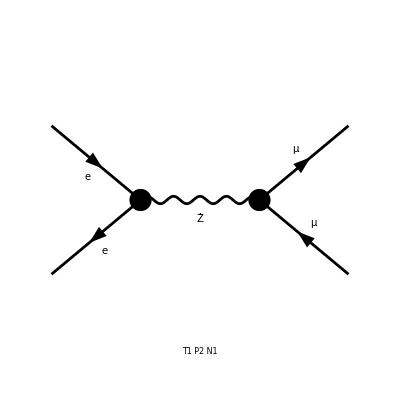

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

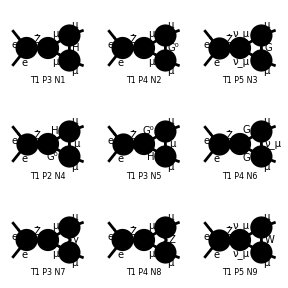

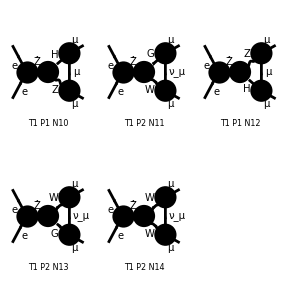

```mathematica
Paint[fieldsBorn];
Paint[fields1L];
```

## Manipulations

### Master Integral and Coefficients

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m");
Length[masters]
```

34

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,14}]
```

### Equal masters

```mathematica
Do[
If[sameIntegral[masters[[i]],masters[[j]]]&&i<j,
Print[ToString[i]<>" "<>ToString[j]]
],
{i,Length[masters]},{j,Length[masters]}]
```

3 9

3 33

4 6

9 33

19 26

19 34

26 34

### Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m")  ;
AReplace={gAl->-Ql,gAu->-Qu,gAd->-Qd};
ZReplace={gZlL->(I3l-Ql*sw^2)/(cw*sw),gZlR->(-Ql*sw^2)/(cw*sw),gZNL->(I3N)/(cw*sw),gZuL->(I3u-(Qu*sw^2))/(cw*sw),gZuR->(-Qu*sw^2)/(cw*sw),gZdL->(I3d-(Qd*sw^2))/(cw*sw),gZdR->(-Qd*sw^2)/(cw*sw)};
```

```mathematica
electronParameters={I3l1->-1/2,Ql1->-1}
```

{I3l1→-1/2,Ql1→-1}

### Born Squared matrix element

```mathematica
myAmpBorn=<<(NotebookDirectory[]<>"feynArts_amplitudes/BornAmplitudes.m")
```

{v̄[p2,0].(ⅈ EL (gZlL[1] ga[Lor1].om_-+gZlR[1] ga[Lor1].om_+)).u[p1,0] ū[k1,MM].(ⅈ EL (gZlL[2] ga[Lor2].om_-+gZlR[2] ga[Lor2].om_+)).v[k2,MM] g[Lor1,Lor2] 1/(-MZ^2+(k1+k2)^2)}

```mathematica
smBorn=AmpSquare[myAmpBorn,myAmpBorn]
```

{1/(4 (mz^2-s)^2)EL^4 (4 mm^4 (gZlL[1]^2+gZlR[1]^2) (gZlL[2]^2+gZlR[2]^2)+4 t^2 (gZlL[1]^2+gZlR[1]^2) (gZlL[2]^2+gZlR[2]^2)+(-2+d) s^2 (gZlL[1]^2 ((-2+d) gZlL[2]^2-(-4+d) gZlR[2]^2)+gZlR[1]^2 (-(-4+d) gZlL[2]^2+(-2+d) gZlR[2]^2))+2 s (2 (-2+d) mm^2 gZlL[2] (gZlL[1]^2+gZlR[1]^2) gZlR[2]+t gZlL[1]^2 ((8-5 d+d^2) gZlL[2]^2-(4-5 d+d^2) gZlR[2]^2)+t gZlR[1]^2 (-(4-5 d+d^2) gZlL[2]^2+(8-5 d+d^2) gZlR[2]^2))-2 mm^2 (4 t (gZlL[1]^2+gZlR[1]^2) (gZlL[2]^2+gZlR[2]^2)+(-2+d) s (gZlL[1]^2 ((-2+d) gZlL[2]^2-(-4+d) gZlR[2]^2)+gZlR[1]^2 (-(-4+d) gZlL[2]^2+(-2+d) gZlR[2]^2))))}

```mathematica
smBornR=smBorn/.parameterReplace/.electronParameters//Expand//FullSimplify
```

{1/(16 CW^4 (mz^2-s)^2 SW^4)EL^4 (-2 I3l2 Ql2 SW^2 (4 mm^4 (1-4 SW^2+8 SW^4)+(-2+d) s^2 (-2+d-4 (-2+d) SW^2+8 SW^4)+2 s (8-5 d+d^2-4 (8+(-5+d) d) SW^2+16 SW^4) t+4 (1-4 SW^2+8 SW^4) t^2+2 mm^2 ((-3+d) (-2+d) s (-1+4 SW^2)-4 (1-4 SW^2+8 SW^4) t))+I3l2^2 (4 mm^4 (1-4 SW^2+8 SW^4)+(-2+d) s^2 (-2+d-4 (-2+d) SW^2+8 SW^4)+2 s (8-5 d+d^2-4 (8+(-5+d) d) SW^2+16 SW^4) t+4 (1-4 SW^2+8 SW^4) t^2+2 mm^2 ((-2+d) s (2-d+4 (-2+d) SW^2-8 SW^4)-4 (1-4 SW^2+8 SW^4) t))+2 Ql2^2 SW^4 (1-4 SW^2+8 SW^4) ((-2+d) s^2+4 (mm^4-2 mm^2 t+t (s+t))))}

```mathematica
prefactor=EL^4/(16cw^4 (mz^2-s)^2sw^4)
```

EL^4/(16 cw^4 (mz^2-s)^2 sw^4)

### Parameter replace

```mathematica
diagramCoefficientsR=diagramCoefficients/.parameterReplace/.electronParameters;
```

Save result

```mathematica
diagramCoefficientsR>>(NotebookDirectory[]<>"coefficients/coefficientsR.m");
```

Load result

```mathematica
diagramCoefficientsR=<<(NotebookDirectory[]<>"coefficients/coefficientsR.m");
```

### Remove Prefactor

```mathematica
smBornA=smBornR/prefactor
```

{1/(CW^4 SW^4)cw^4 sw^4 (-2 I3l2 Ql2 SW^2 (4 mm^4 (1-4 SW^2+8 SW^4)+(-2+d) s^2 (-2+d-4 (-2+d) SW^2+8 SW^4)+2 s (8-5 d+d^2-4 (8+(-5+d) d) SW^2+16 SW^4) t+4 (1-4 SW^2+8 SW^4) t^2+2 mm^2 ((-3+d) (-2+d) s (-1+4 SW^2)-4 (1-4 SW^2+8 SW^4) t))+I3l2^2 (4 mm^4 (1-4 SW^2+8 SW^4)+(-2+d) s^2 (-2+d-4 (-2+d) SW^2+8 SW^4)+2 s (8-5 d+d^2-4 (8+(-5+d) d) SW^2+16 SW^4) t+4 (1-4 SW^2+8 SW^4) t^2+2 mm^2 ((-2+d) s (2-d+4 (-2+d) SW^2-8 SW^4)-4 (1-4 SW^2+8 SW^4) t))+2 Ql2^2 SW^4 (1-4 SW^2+8 SW^4) ((-2+d) s^2+4 (mm^4-2 mm^2 t+t (s+t))))}

```mathematica
diagramCoefficientsA=diagramCoefficientsR/prefactor
```

{1}
 |  |  |  |

```mathematica
diagramCoefficientsA=diagramCoefficientsA//Expand//Simplify
```

{1}
 |  |  |  |

Save result

```mathematica
diagramCoefficientsA>>(NotebookDirectory[]<>"coefficients/coefficientsA.m");
```

Load result

```mathematica
diagramCoefficientsA=<<(NotebookDirectory[]<>"coefficients/coefficientsA.m");
```

```mathematica
diagramCoefficientsA[[7]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/(8 CW^4 π^4 SW^4)ⅈ cw^4 EL^2 Ql2^2 (2 mm^2-s) sw^4 (2 Ql2^2 SW^4 (1-4 SW^2+8 SW^4) (4 mm^4+(-2+d) s^2-8 mm^2 t+4 s t+4 t^2)-2 I3l2 Ql2 SW^2 (4 mm^4 (1-4 SW^2+8 SW^4)+s^2 (4-4 d+d^2-16 SW^2+16 d SW^2-4 d^2 SW^2-16 SW^4+8 d SW^4)+2 s (8-5 d+d^2-32 SW^2+20 d SW^2-4 d^2 SW^2+16 SW^4) t+4 (1-4 SW^2+8 SW^4) t^2+2 mm^2 ((6-5 d+d^2) s (-1+4 SW^2)-4 (1-4 SW^2+8 SW^4) t))+I3l2^2 (4 mm^4 (1-4 SW^2+8 SW^4)+s^2 (4-4 d+d^2-16 SW^2+16 d SW^2-4 d^2 SW^2-16 SW^4+8 d SW^4)+2 s (8-5 d+d^2-32 SW^2+20 d SW^2-4 d^2 SW^2+16 SW^4) t+4 (1-4 SW^2+8 SW^4) t^2+2 mm^2 (s (d^2 (-1+4 SW^2)-4 d (-1+4 SW^2+2 SW^4)+4 (-1+4 SW^2+4 SW^4))-4 (1-4 SW^2+8 SW^4) t))),-1/(4 CW^4 π^4 (4 mm^2-s) SW^4)ⅈ cw^4 EL^2 Ql2^2 sw^4 (2 Ql2^2 SW^4 (1-4 SW^2+8 SW^4) (8 mm^6-4 mm^4 (s+4 t)+4 mm^2 ((-2+d) s^2+4 s t+2 t^2)-s ((-2+d) s^2+4 s t+4 t^2))+I3l2^2 (8 mm^6 (1-4 SW^2+8 SW^4)+2 mm^4 (s (3 d^2 (-1+4 SW^2)+d (13-52 SW^2-16 SW^4)+16 (-1+4 SW^2+SW^4))-8 (1-4 SW^2+8 SW^4) t)+s (s^2 (d^2 (-1+4 SW^2)-4 d (-1+4 SW^2+2 SW^4)+4 (-1+4 SW^2+4 SW^4))+2 s (d (5-20 SW^2)+d^2 (-1+4 SW^2)-8 (1-4 SW^2+2 SW^4)) t-4 (1-4 SW^2+8 SW^4) t^2)+mm^2 (-5 s^2 (d^2 (-1+4 SW^2)-4 d (-1+4 SW^2+2 SW^4)+4 (-1+4 SW^2+4 SW^4))+2 s (26-104 SW^2+64 SW^4+d^2 (3-12 SW^2)+15 d (-1+4 SW^2)) t+8 (1-4 SW^2+8 SW^4) t^2))-2 I3l2 Ql2 SW^2 (8 mm^6 (1-4 SW^2+8 SW^4)+2 mm^4 (s (d (15-60 SW^2)+3 d^2 (-1+4 SW^2)-4 (5-20 SW^2+4 SW^4))-8 (1-4 SW^2+8 SW^4) t)+s (s^2 (d^2 (-1+4 SW^2)-4 d (-1+4 SW^2+2 SW^4)+4 (-1+4 SW^2+4 SW^4))+2 s (d (5-20 SW^2)+d^2 (-1+4 SW^2)-8 (1-4 SW^2+2 SW^4)) t-4 (1-4 SW^2+8 SW^4) t^2)+mm^2 (s^2 (22-88 SW^2-64 SW^4+d^2 (5-20 SW^2)+d (-21+84 SW^2+32 SW^4))+2 s (26-104 SW^2+64 SW^4+d^2 (3-12 SW^2)+15 d (-1+4 SW^2)) t+8 (1-4 SW^2+8 SW^4) t^2))),1/(16 CW^4 π^4 (4 mm^2-s) SW^4)ⅈ cw^4 EL^2 Ql2^2 sw^4 (2 Ql2^2 SW^4 (1-4 SW^2+8 SW^4) (32 mm^6+4 mm^4 ((-7+d) s-16 t)-4 mm^2 ((14-9 d+d^2) s^2+2 (-11+d) s t-8 t^2)+(-7+d) s ((-2+d) s^2+4 s t+4 t^2))-2 I3l2 Ql2 SW^2 (32 mm^6 (1-4 SW^2+8 SW^4)-4 mm^4 (s (79-316 SW^2+56 SW^4+d^2 (22-88 SW^2)+d^3 (-2+8 SW^2)+d (-73+292 SW^2-8 SW^4))+16 (1-4 SW^2+8 SW^4) t)-(-7+d) s (s^2 (d^2 (-1+4 SW^2)-4 d (-1+4 SW^2+2 SW^4)+4 (-1+4 SW^2+4 SW^4))+2 s (d (5-20 SW^2)+d^2 (-1+4 SW^2)-8 (1-4 SW^2+2 SW^4)) t-4 (1-4 SW^2+8 SW^4) t^2)+2 mm^2 (s^2 (86-344 SW^2-224 SW^4+3 d^3 (-1+4 SW^2)-16 d^2 (-2+8 SW^2+SW^4)+d (-95+380 SW^2+144 SW^4))+4 s (47-188 SW^2+88 SW^4+d^2 (11-44 SW^2)+d^3 (-1+4 SW^2)+d (-37+148 SW^2-8 SW^4)) t+16 (1-4 SW^2+8 SW^4) t^2))+I3l2^2 (-8 (-7+d) mm^6 (1-4 SW^2+8 SW^4)-4 mm^4 (s (59-236 SW^2-104 SW^4+d^3 (-2+8 SW^2)-4 d^2 (-5+20 SW^2+4 SW^4)+d (-59+236 SW^2+104 SW^4))-4 (-7+d) (1-4 SW^2+8 SW^4) t)-(-7+d) s (s^2 (d^2 (-1+4 SW^2)-4 d (-1+4 SW^2+2 SW^4)+4 (-1+4 SW^2+4 SW^4))+2 s (d (5-20 SW^2)+d^2 (-1+4 SW^2)-8 (1-4 SW^2+2 SW^4)) t-4 (1-4 SW^2+8 SW^4) t^2)+2 mm^2 (s^2 (3 d^3 (-1+4 SW^2)+d^2 (31-124 SW^2-24 SW^4)-76 (-1+4 SW^2+4 SW^4)+8 d (-11+44 SW^2+25 SW^4))+4 s (50-200 SW^2+112 SW^4+d^2 (11-44 SW^2)+d^3 (-1+4 SW^2)-2 d (19-76 SW^2+8 SW^4)) t-4 (-7+d) (1-4 SW^2+8 SW^4) t^2))),-(ⅈ cw^4 (-2+d) EL^2 Ql2^2 sw^4 (I3l2-2 Ql2 SW^2)^2 (1-4 SW^2+8 SW^4) (mm^4-2 mm^2 t+t (s+t)))/(4 CW^4 π^4 (4 mm^2-s) SW^4)}

## Terms

```mathematica
coeffQ1=Coefficient[diagramCoefficientsA,Ql2,1];
coeffQ2=Coefficient[diagramCoefficientsA,Ql2,2];
coeffQ3=Coefficient[diagramCoefficientsA,Ql2,3];
coeffQ4=Coefficient[diagramCoefficientsA,Ql2,4];
```

```mathematica
nullCoeffList={};
Do[nullCoeffList=Append[nullCoeffList,0],Length[masters]];
nullCoeffList
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Do[If[coeffQ1[[i]]=!=nullCoeffList,Print[i]],{i,Length[coeffQ1]}]
```

1

2

3

4

5

6

8

9

10

11

12

13

14

```mathematica
Do[If[coeffQ2[[i]]=!=nullCoeffList,Print[i]],{i,Length[coeffQ2]}]
```

1

2

7

8

10

12

```mathematica
Do[If[coeffQ3[[i]]=!=nullCoeffList,Print[i]],{i,Length[coeffQ3]}]
```

7

8

```mathematica
Do[If[coeffQ4[[i]]=!=nullCoeffList,Print[i]],{i,Length[coeffQ4]}]
```

7

8

## Q^4 terms

```mathematica
coeffQ4[[7]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/(8 CW^4 π^4 SW^4)ⅈ cw^4 EL^2 (2 mm^2-s) sw^4 (8 mm^4 SW^4-4 s^2 SW^4+2 d s^2 SW^4-32 mm^4 SW^6+16 s^2 SW^6-8 d s^2 SW^6+64 mm^4 SW^8-32 s^2 SW^8+16 d s^2 SW^8-16 mm^2 SW^4 t+8 s SW^4 t+64 mm^2 SW^6 t-32 s SW^6 t-128 mm^2 SW^8 t+64 s SW^8 t+8 SW^4 t^2-32 SW^6 t^2+64 SW^8 t^2),-1/(4 CW^4 π^4 (4 mm^2-s) SW^4)ⅈ cw^4 EL^2 sw^4 (16 mm^6 SW^4-8 mm^4 s SW^4-16 mm^2 s^2 SW^4+8 d mm^2 s^2 SW^4+4 s^3 SW^4-2 d s^3 SW^4-64 mm^6 SW^6+32 mm^4 s SW^6+64 mm^2 s^2 SW^6-32 d mm^2 s^2 SW^6-16 s^3 SW^6+8 d s^3 SW^6+128 mm^6 SW^8-64 mm^4 s SW^8-128 mm^2 s^2 SW^8+64 d mm^2 s^2 SW^8+32 s^3 SW^8-16 d s^3 SW^8-32 mm^4 SW^4 t+32 mm^2 s SW^4 t-8 s^2 SW^4 t+128 mm^4 SW^6 t-128 mm^2 s SW^6 t+32 s^2 SW^6 t-256 mm^4 SW^8 t+256 mm^2 s SW^8 t-64 s^2 SW^8 t+16 mm^2 SW^4 t^2-8 s SW^4 t^2-64 mm^2 SW^6 t^2+32 s SW^6 t^2+128 mm^2 SW^8 t^2-64 s SW^8 t^2),1/(16 CW^4 π^4 (4 mm^2-s) SW^4)ⅈ cw^4 EL^2 sw^4 (64 mm^6 SW^4-56 mm^4 s SW^4+8 d mm^4 s SW^4-112 mm^2 s^2 SW^4+72 d mm^2 s^2 SW^4-8 d^2 mm^2 s^2 SW^4+28 s^3 SW^4-18 d s^3 SW^4+2 d^2 s^3 SW^4-256 mm^6 SW^6+224 mm^4 s SW^6-32 d mm^4 s SW^6+448 mm^2 s^2 SW^6-288 d mm^2 s^2 SW^6+32 d^2 mm^2 s^2 SW^6-112 s^3 SW^6+72 d s^3 SW^6-8 d^2 s^3 SW^6+512 mm^6 SW^8-448 mm^4 s SW^8+64 d mm^4 s SW^8-896 mm^2 s^2 SW^8+576 d mm^2 s^2 SW^8-64 d^2 mm^2 s^2 SW^8+224 s^3 SW^8-144 d s^3 SW^8+16 d^2 s^3 SW^8-128 mm^4 SW^4 t+176 mm^2 s SW^4 t-16 d mm^2 s SW^4 t-56 s^2 SW^4 t+8 d s^2 SW^4 t+512 mm^4 SW^6 t-704 mm^2 s SW^6 t+64 d mm^2 s SW^6 t+224 s^2 SW^6 t-32 d s^2 SW^6 t-1024 mm^4 SW^8 t+1408 mm^2 s SW^8 t-128 d mm^2 s SW^8 t-448 s^2 SW^8 t+64 d s^2 SW^8 t+64 mm^2 SW^4 t^2-56 s SW^4 t^2+8 d s SW^4 t^2-256 mm^2 SW^6 t^2+224 s SW^6 t^2-32 d s SW^6 t^2+512 mm^2 SW^8 t^2-448 s SW^8 t^2+64 d s SW^8 t^2),-(ⅈ cw^4 (-2+d) EL^2 sw^4 (1-4 SW^2+8 SW^4) (mm^4-2 mm^2 t+t (s+t)))/(CW^4 π^4 (4 mm^2-s))}

```mathematica
coeffQ4[[8]]
```

{0,0,0,0,0,-(ⅈ cw^4 (-2+d) EL^2 sw^4 SW^2 (1-4 SW^2+8 SW^4) (mm^4-2 mm^2 t+t (s+t)))/(CW^6 π^4 (4 mm^2-s)),(ⅈ cw^4 (-2+d) EL^2 sw^4 SW^2 (1-4 SW^2+8 SW^4) (mm^4-2 mm^2 t+t (s+t)))/(CW^6 π^4 (4 mm^2-s)),-1/(4 CW^6 π^4 (-4 mm^2+s)^2)ⅈ cw^4 EL^2 sw^4 SW^2 (1-4 SW^2+8 SW^4) (64 mm^8+16 mm^6 (2 (-2+d) mz^2-3 s-8 t)-4 mm^4 (mz^2 ((-3+d) s+16 (-2+d) t)-2 ((-7+4 d) s^2+20 s t+8 t^2))+s (2 s ((-2+d) s^2+4 s t+4 t^2)+mz^2 ((-2+d) s^2-4 (-3+d) s t-4 (-3+d) t^2))-4 mm^2 (4 s ((-2+d) s^2+4 s t+3 t^2)+mz^2 ((-2+d) s^2+2 (11-5 d) s t-8 (-2+d) t^2))),1/(8 CW^6 π^4 (-4 mm^2+s)^2)ⅈ cw^4 EL^2 sw^4 SW^2 (1-4 SW^2+8 SW^4) (128 mm^8+16 mm^6 (2 (-2+d) mz^2+(-9+d) s-16 t)+s (2 mz^2-(-7+d) s) ((-2+d) s^2+4 s t+4 t^2)+4 mm^4 ((-49+35 d-4 d^2) s^2-8 (-13+d) s t+32 t^2+2 mz^2 (s-8 (-2+d) t))-8 mm^2 (-s ((14-9 d+d^2) s^2+(-25+3 d) s t+2 (-9+d) t^2)+mz^2 ((-2+d) s^2+2 (5-2 d) s t-4 (-2+d) t^2))),-1/(8 CW^6 π^4 (-4 mm^2+s)^2)ⅈ cw^4 EL^2 sw^4 SW^2 (1-4 SW^2+8 SW^4) (256 mm^10-s (2 mz^4-(-8+d) mz^2 s+2 s^2) ((-2+d) s^2+4 s t+4 t^2)+64 mm^8 ((-4+d) mz^2-4 (s+2 t))-16 mm^6 (2 (-2+d) mz^4+(3-4 d) s^2-48 s t-16 t^2+2 mz^2 ((-6+d) s+4 (-4+d) t))-4 mm^4 (2 mz^4 (s-8 (-2+d) t)+2 s ((-15+8 d) s^2+52 s t+32 t^2)+mz^2 ((-56+39 d-4 d^2) s^2-32 (-5+d) s t-16 (-4+d) t^2))+4 mm^2 (s^2 (5 (-2+d) s^2+24 s t+20 t^2)-2 mz^2 s ((16-10 d+d^2) s^2+(-32+5 d) s t+4 (-6+d) t^2)+2 mz^4 ((-2+d) s^2+2 (5-2 d) s t-4 (-2+d) t^2))),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
coeffQ3[[7]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/(8 CW^4 π^4 SW^4)ⅈ cw^4 EL^2 (2 mm^2-s) sw^4 (-8 I3l2 mm^4 SW^2+24 I3l2 mm^2 s SW^2-20 d I3l2 mm^2 s SW^2+4 d^2 I3l2 mm^2 s SW^2-8 I3l2 s^2 SW^2+8 d I3l2 s^2 SW^2-2 d^2 I3l2 s^2 SW^2+32 I3l2 mm^4 SW^4-96 I3l2 mm^2 s SW^4+80 d I3l2 mm^2 s SW^4-16 d^2 I3l2 mm^2 s SW^4+32 I3l2 s^2 SW^4-32 d I3l2 s^2 SW^4+8 d^2 I3l2 s^2 SW^4-64 I3l2 mm^4 SW^6+32 I3l2 s^2 SW^6-16 d I3l2 s^2 SW^6+16 I3l2 mm^2 SW^2 t-32 I3l2 s SW^2 t+20 d I3l2 s SW^2 t-4 d^2 I3l2 s SW^2 t-64 I3l2 mm^2 SW^4 t+128 I3l2 s SW^4 t-80 d I3l2 s SW^4 t+16 d^2 I3l2 s SW^4 t+128 I3l2 mm^2 SW^6 t-64 I3l2 s SW^6 t-8 I3l2 SW^2 t^2+32 I3l2 SW^4 t^2-64 I3l2 SW^6 t^2),-1/(4 CW^4 π^4 (4 mm^2-s) SW^4)ⅈ cw^4 EL^2 sw^4 (-16 I3l2 mm^6 SW^2+80 I3l2 mm^4 s SW^2-60 d I3l2 mm^4 s SW^2+12 d^2 I3l2 mm^4 s SW^2-44 I3l2 mm^2 s^2 SW^2+42 d I3l2 mm^2 s^2 SW^2-10 d^2 I3l2 mm^2 s^2 SW^2+8 I3l2 s^3 SW^2-8 d I3l2 s^3 SW^2+2 d^2 I3l2 s^3 SW^2+64 I3l2 mm^6 SW^4-320 I3l2 mm^4 s SW^4+240 d I3l2 mm^4 s SW^4-48 d^2 I3l2 mm^4 s SW^4+176 I3l2 mm^2 s^2 SW^4-168 d I3l2 mm^2 s^2 SW^4+40 d^2 I3l2 mm^2 s^2 SW^4-32 I3l2 s^3 SW^4+32 d I3l2 s^3 SW^4-8 d^2 I3l2 s^3 SW^4-128 I3l2 mm^6 SW^6+64 I3l2 mm^4 s SW^6+128 I3l2 mm^2 s^2 SW^6-64 d I3l2 mm^2 s^2 SW^6-32 I3l2 s^3 SW^6+16 d I3l2 s^3 SW^6+32 I3l2 mm^4 SW^2 t-104 I3l2 mm^2 s SW^2 t+60 d I3l2 mm^2 s SW^2 t-12 d^2 I3l2 mm^2 s SW^2 t+32 I3l2 s^2 SW^2 t-20 d I3l2 s^2 SW^2 t+4 d^2 I3l2 s^2 SW^2 t-128 I3l2 mm^4 SW^4 t+416 I3l2 mm^2 s SW^4 t-240 d I3l2 mm^2 s SW^4 t+48 d^2 I3l2 mm^2 s SW^4 t-128 I3l2 s^2 SW^4 t+80 d I3l2 s^2 SW^4 t-16 d^2 I3l2 s^2 SW^4 t+256 I3l2 mm^4 SW^6 t-256 I3l2 mm^2 s SW^6 t+64 I3l2 s^2 SW^6 t-16 I3l2 mm^2 SW^2 t^2+8 I3l2 s SW^2 t^2+64 I3l2 mm^2 SW^4 t^2-32 I3l2 s SW^4 t^2-128 I3l2 mm^2 SW^6 t^2+64 I3l2 s SW^6 t^2),1/(16 CW^4 π^4 (4 mm^2-s) SW^4)ⅈ cw^4 EL^2 sw^4 (-64 I3l2 mm^6 SW^2+632 I3l2 mm^4 s SW^2-584 d I3l2 mm^4 s SW^2+176 d^2 I3l2 mm^4 s SW^2-16 d^3 I3l2 mm^4 s SW^2-344 I3l2 mm^2 s^2 SW^2+380 d I3l2 mm^2 s^2 SW^2-128 d^2 I3l2 mm^2 s^2 SW^2+12 d^3 I3l2 mm^2 s^2 SW^2+56 I3l2 s^3 SW^2-64 d I3l2 s^3 SW^2+22 d^2 I3l2 s^3 SW^2-2 d^3 I3l2 s^3 SW^2+256 I3l2 mm^6 SW^4-2528 I3l2 mm^4 s SW^4+2336 d I3l2 mm^4 s SW^4-704 d^2 I3l2 mm^4 s SW^4+64 d^3 I3l2 mm^4 s SW^4+1376 I3l2 mm^2 s^2 SW^4-1520 d I3l2 mm^2 s^2 SW^4+512 d^2 I3l2 mm^2 s^2 SW^4-48 d^3 I3l2 mm^2 s^2 SW^4-224 I3l2 s^3 SW^4+256 d I3l2 s^3 SW^4-88 d^2 I3l2 s^3 SW^4+8 d^3 I3l2 s^3 SW^4-512 I3l2 mm^6 SW^6+448 I3l2 mm^4 s SW^6-64 d I3l2 mm^4 s SW^6+896 I3l2 mm^2 s^2 SW^6-576 d I3l2 mm^2 s^2 SW^6+64 d^2 I3l2 mm^2 s^2 SW^6-224 I3l2 s^3 SW^6+144 d I3l2 s^3 SW^6-16 d^2 I3l2 s^3 SW^6+128 I3l2 mm^4 SW^2 t-752 I3l2 mm^2 s SW^2 t+592 d I3l2 mm^2 s SW^2 t-176 d^2 I3l2 mm^2 s SW^2 t+16 d^3 I3l2 mm^2 s SW^2 t+224 I3l2 s^2 SW^2 t-172 d I3l2 s^2 SW^2 t+48 d^2 I3l2 s^2 SW^2 t-4 d^3 I3l2 s^2 SW^2 t-512 I3l2 mm^4 SW^4 t+3008 I3l2 mm^2 s SW^4 t-2368 d I3l2 mm^2 s SW^4 t+704 d^2 I3l2 mm^2 s SW^4 t-64 d^3 I3l2 mm^2 s SW^4 t-896 I3l2 s^2 SW^4 t+688 d I3l2 s^2 SW^4 t-192 d^2 I3l2 s^2 SW^4 t+16 d^3 I3l2 s^2 SW^4 t+1024 I3l2 mm^4 SW^6 t-1408 I3l2 mm^2 s SW^6 t+128 d I3l2 mm^2 s SW^6 t+448 I3l2 s^2 SW^6 t-64 d I3l2 s^2 SW^6 t-64 I3l2 mm^2 SW^2 t^2+56 I3l2 s SW^2 t^2-8 d I3l2 s SW^2 t^2+256 I3l2 mm^2 SW^4 t^2-224 I3l2 s SW^4 t^2+32 d I3l2 s SW^4 t^2-512 I3l2 mm^2 SW^6 t^2+448 I3l2 s SW^6 t^2-64 d I3l2 s SW^6 t^2),(ⅈ cw^4 (-2+d) EL^2 I3l2 sw^4 (1-4 SW^2+8 SW^4) (mm^4-2 mm^2 t+t (s+t)))/(CW^4 π^4 (4 mm^2-s) SW^2)}

```mathematica
coeffQ3[[8]]
```

{0,0,0,0,0,(2 ⅈ cw^4 (-2+d) EL^2 I3l2 sw^4 (1-4 SW^2+8 SW^4) (mm^4-2 mm^2 t+t (s+t)))/(CW^6 π^4 (4 mm^2-s)),-(2 ⅈ cw^4 (-2+d) EL^2 I3l2 sw^4 (1-4 SW^2+8 SW^4) (mm^4-2 mm^2 t+t (s+t)))/(CW^6 π^4 (4 mm^2-s)),1/(2 CW^6 π^4 (-4 mm^2+s)^2)ⅈ cw^4 EL^2 I3l2 sw^4 (64 mm^8 (1-4 SW^2+8 SW^4)+8 mm^6 (4 (-2+d) mz^2 (1-4 SW^2+8 SW^4)+s (d^2 (4-16 SW^2)-12 (1-2 SW^2)^2+d (-1+4 SW^2)+d^3 (-1+4 SW^2))-16 (1-4 SW^2+8 SW^4) t)-2 mm^4 (s^2 (-38+152 SW^2+224 SW^4+d^2 (4-16 SW^2)+3 d^3 (-1+4 SW^2)+d (21-84 SW^2-128 SW^4))+4 s (d^2 (4-16 SW^2)+d (-1+4 SW^2)+d^3 (-1+4 SW^2)-2 (13-52 SW^2+80 SW^4)) t-32 (1-4 SW^2+8 SW^4) t^2+2 mz^2 (s (d^2 (-2+8 SW^2)+d (11-44 SW^2+8 SW^4)-3 (5-20 SW^2+8 SW^4))+16 (-2+d) (1-4 SW^2+8 SW^4) t))+s (2 s (s^2 (4-4 d+d^2-16 SW^2+16 d SW^2-4 d^2 SW^2-16 SW^4+8 d SW^4)+2 s (8-5 d+d^2-32 SW^2+20 d SW^2-4 d^2 SW^2+16 SW^4) t+4 (1-4 SW^2+8 SW^4) t^2)+mz^2 (s^2 (d^2 (1-4 SW^2)+4 d (-1+4 SW^2+2 SW^4)-4 (-1+4 SW^2+4 SW^4))+2 s (d^2 (1-4 SW^2)+12 (1-2 SW^2)^2+d (-7+28 SW^2-16 SW^4)) t-4 (-3+d) (1-4 SW^2+8 SW^4) t^2))+mm^2 (s (s^2 (-46+184 SW^2+256 SW^4+8 d^2 (-1+4 SW^2)+d^3 (-1+4 SW^2)+d (43-172 SW^2-128 SW^4))+2 s (-86+344 SW^2-256 SW^4-39 d (-1+4 SW^2)+4 d^2 (-1+4 SW^2)+d^3 (-1+4 SW^2)) t-48 (1-4 SW^2+8 SW^4) t^2)+2 mz^2 (s^2 (-14+56 SW^2+32 SW^4+3 d^2 (-1+4 SW^2)+d (13-52 SW^2-16 SW^4))+4 s (-17+68 SW^2-88 SW^4+10 d (1-2 SW^2)^2+d^2 (-1+4 SW^2)) t+16 (-2+d) (1-4 SW^2+8 SW^4) t^2))),-1/(4 CW^6 π^4 (-4 mm^2+s)^2)ⅈ cw^4 EL^2 I3l2 sw^4 (128 mm^8 (1-4 SW^2+8 SW^4)+16 mm^6 (2 (-2+d) mz^2 (1-4 SW^2+8 SW^4)+s (-51+204 SW^2-72 SW^4+d^3 (1-4 SW^2)+12 d^2 (-1+4 SW^2)+2 d (21-84 SW^2+4 SW^4))-16 (1-4 SW^2+8 SW^4) t)+s (-2 mz^2+(-7+d) s) (s^2 (d^2 (-1+4 SW^2)-4 d (-1+4 SW^2+2 SW^4)+4 (-1+4 SW^2+4 SW^4))+2 s (d (5-20 SW^2)+d^2 (-1+4 SW^2)-8 (1-4 SW^2+2 SW^4)) t-4 (1-4 SW^2+8 SW^4) t^2)-4 mm^4 (s^2 (d^3 (5-20 SW^2)+8 d^2 (-7+28 SW^2+4 SW^4)-10 d (-17+68 SW^2+28 SW^4)+7 (-23+92 SW^2+56 SW^4))-4 s (d^2 (12-48 SW^2)+d^3 (-1+4 SW^2)+d (-43+172 SW^2-16 SW^4)+4 (17-68 SW^2+52 SW^4)) t-32 (1-4 SW^2+8 SW^4) t^2+2 mz^2 (s (-13+52 SW^2-8 SW^4+d (10-40 SW^2)+d^2 (-2+8 SW^2))+8 (-2+d) (1-4 SW^2+8 SW^4) t))+4 mm^2 (s (2 s^2 (d^3 (1-4 SW^2)+28 (-1+4 SW^2+4 SW^4)+d^2 (-11+44 SW^2+8 SW^4)-8 d (-4+16 SW^2+9 SW^4))+s (d^3 (3-12 SW^2)+36 d^2 (-1+4 SW^2)+3 d (43-172 SW^2+16 SW^4)-16 (11-44 SW^2+25 SW^4)) t+4 (-9+d) (1-4 SW^2+8 SW^4) t^2)+mz^2 (s^2 (-14+56 SW^2+32 SW^4+3 d^2 (-1+4 SW^2)+d (13-52 SW^2-16 SW^4))+4 s (-11+44 SW^2-40 SW^4+d^2 (-1+4 SW^2)+d (7-28 SW^2+16 SW^4)) t+8 (-2+d) (1-4 SW^2+8 SW^4) t^2))),1/(4 CW^6 π^4 (-4 mm^2+s)^2)ⅈ cw^4 EL^2 I3l2 sw^4 (256 mm^10 (1-4 SW^2+8 SW^4)+64 mm^8 ((-4+d) mz^2 (1-4 SW^2+8 SW^4)+s (-10+40 SW^2-32 SW^4+d (5-20 SW^2)+d^2 (-1+4 SW^2))-8 (1-4 SW^2+8 SW^4) t)+s (2 mz^4-(-8+d) mz^2 s+2 s^2) (s^2 (d^2 (-1+4 SW^2)-4 d (-1+4 SW^2+2 SW^4)+4 (-1+4 SW^2+4 SW^4))+2 s (d (5-20 SW^2)+d^2 (-1+4 SW^2)-8 (1-4 SW^2+2 SW^4)) t-4 (1-4 SW^2+8 SW^4) t^2)-16 mm^6 (2 (-2+d) mz^4 (1-4 SW^2+8 SW^4)+s^2 (8 d^2 (-1+4 SW^2)-4 d (-9+36 SW^2+8 SW^4)+3 (-15+60 SW^2+8 SW^4))-4 s (18-72 SW^2+96 SW^4+d^2 (1-4 SW^2)+5 d (-1+4 SW^2)) t-16 (1-4 SW^2+8 SW^4) t^2+mz^2 (s (-66+264 SW^2-96 SW^4+d^3 (1-4 SW^2)+14 d^2 (-1+4 SW^2)+d (53-212 SW^2+16 SW^4))+8 (-4+d) (1-4 SW^2+8 SW^4) t))+4 mm^4 (2 mz^4 (s (-13+52 SW^2-8 SW^4+d (10-40 SW^2)+d^2 (-2+8 SW^2))+8 (-2+d) (1-4 SW^2+8 SW^4) t)+s (s^2 (21 d^2 (-1+4 SW^2)+d (89-356 SW^2-128 SW^4)+48 (-2+8 SW^2+5 SW^4))+8 s (-31+124 SW^2-104 SW^4+d (15-60 SW^2)+3 d^2 (-1+4 SW^2)) t-64 (1-4 SW^2+8 SW^4) t^2)+mz^2 (s^2 (-202+808 SW^2+448 SW^4+d^3 (5-20 SW^2)+d (206-824 SW^2-312 SW^4)+32 d^2 (-2+8 SW^2+SW^4))-4 s (94-376 SW^2+320 SW^4+d^2 (14-56 SW^2)+d^3 (-1+4 SW^2)+d (-59+236 SW^2-64 SW^4)) t+16 (-4+d) (1-4 SW^2+8 SW^4) t^2))-2 mm^2 (s^2 (s^2 (11 d^2 (-1+4 SW^2)-5 d (-9+36 SW^2+16 SW^4)+2 (-23+92 SW^2+80 SW^4))+6 s (-26+104 SW^2-64 SW^4+d (15-60 SW^2)+3 d^2 (-1+4 SW^2)) t-40 (1-4 SW^2+8 SW^4) t^2)+mz^2 s (s^2 (-134+536 SW^2+512 SW^4+d^3 (4-16 SW^2)+d (149-596 SW^2-320 SW^4)+d^2 (-49+196 SW^2+32 SW^4))-2 s (214-856 SW^2+512 SW^4-40 d^2 (-1+4 SW^2)+3 d^3 (-1+4 SW^2)+d (-153+612 SW^2-80 SW^4)) t+16 (-6+d) (1-4 SW^2+8 SW^4) t^2)+2 mz^4 (s^2 (-14+56 SW^2+32 SW^4+3 d^2 (-1+4 SW^2)+d (13-52 SW^2-16 SW^4))+4 s (-11+44 SW^2-40 SW^4+d^2 (-1+4 SW^2)+d (7-28 SW^2+16 SW^4)) t+8 (-2+d) (1-4 SW^2+8 SW^4) t^2))),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Not null terms

```mathematica
notZero[0]:=0
notZero[expr_]:=1
```

```mathematica
Map[notZero,coeffQ1,{2}]
```

{{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}

```mathematica
Map[notZero,coeffQ2,{2}]
```

{{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1},{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Map[notZero,coeffQ3,{2}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1},{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Map[notZero,coeffQ4,{2}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1},{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## Analogous Integral Families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2];
]
```

## Functions

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
]
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}]
```